```mathematica
Needs["NoisyQuantumTeleportationBenchmarking`", "C:/Users/pdbru/Desktop/tesis/mathematica/NoisyQuantumTeleportationBenchmarking.wl"]
```

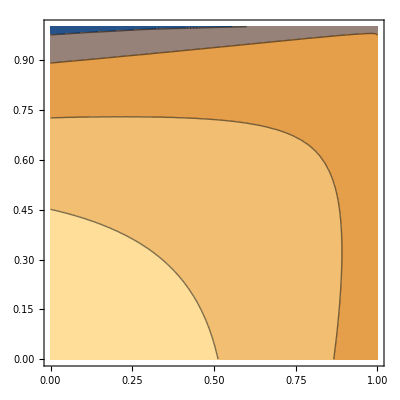

```mathematica
ContourPlot[AvgDistanceOfTeleportation[ADC[pA],ADC[pB], Aff],{pA,0,1},{pB,0,1}]
```

```mathematica
ForAllChannelsAndDistances[Function[{chA, chB, d, AvgDist, PaulisAvg}, 
newStyle[x_]:=x/. l_Line:>Sequence[Opacity[.4],Thick,Dashed,Red,l];

th = GetDistanceThreshold[d];

Print[GraphicsRow[{
ContourPlot[AvgDist[pA,pB],{pA,0,1},{pB,0,1},
FrameLabel->{Style[Subscript[p,a],Black,Italic,24],Style[Subscript[p,b],Black,Italic,24]},
Contours->(Sort[Append[FindDivisions[{#1,#2},#3], GetDistanceThreshold[d]]]&),
ContourLabels->All,
PlotLegends->Automatic, 
PlotLabel-> GetDistanceLabel[d] <> "\nCanal de Alice: " <> GetChannelLabel[chA] <> "\nCanal de Bob: " <> GetChannelLabel[chB],
ImageSize->400
]/. Tooltip[x_,th]:>Tooltip[newStyle[x],th], 
ContourPlot[PaulisAvg[pA,pB],{pA,0,1},{pB,0,1},
FrameLabel->{Style[Subscript[p,a],Black,Italic,24],Style[Subscript[p,b],Black,Italic,24]},
Contours->(Sort[Append[FindDivisions[{#1,#2},#3], GetDistanceThreshold[d]]]&),
ContourLabels->All,
PlotLegends->Automatic, 
PlotLabel-> GetDistanceLabel[d] <> "\nCanal de Alice: " <> GetChannelLabel[chA] <> "\nCanal de Bob: " <> GetChannelLabel[chB]<> "\nPauli Average" ,
ImageSize->400
]/. Tooltip[x_,th]:>Tooltip[newStyle[x],th], 
ContourPlot[Abs[PaulisAvg[pA,pB] - AvgDist[pA,pB]],{pA,0,1},{pB,0,1},
FrameLabel->{Style[Subscript[p,a],Black,Italic,24],Style[Subscript[p,b],Black,Italic,24]},
PlotLegends->Automatic, 
PlotLabel-> GetDistanceLabel[d] <> "\nCanal de Alice: " <> GetChannelLabel[chA] <> "\nCanal de Bob: " <> GetChannelLabel[chB]<> "\nAbsolute averages difference",
ImageSize->400
]
}, 0, ImageSize->Full]];
]]
```

-Graphics-

-Graphics-

-Graphics-

«61 more identical outputs»